```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
simulatorPS[la_,mu_,iniTrans_,simuLen_]:=Module[{simTime,res,state,meanqlen,prevEvTime,nextArr,nextDep,joblist,delsum,nofsamples,i},
simTime=0;
(* Initialisatiom: *)
(* Draw the arrival time from exponential distribution *)
nextArr=RandomVariate[ExponentialDistribution[la]]; 
nextDep=Infinity;
(* set X_0 (queue length) = 0*)
joblist={};
meanqlen=0;
delsum=0;
nofsamples=0;
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextArr; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
If[Length[joblist]>0,
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]],
joblist={} (* else *)
];
(* process arrival event, insert new job in job list *)
joblist=Append[joblist,{simTime,RandomVariate[ExponentialDistribution[mu]]}];
(* sort joblist based on remaining service time *)
joblist=Sort[joblist,#1[[2]]<#2[[2]]&];
(* generate new arrival event, and departure event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[la]];
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
},
{
prevEvTime=simTime; (* save time of previous event *)
simTime=nextDep; (* move time to new event *)
meanqlen+=Length[joblist]*(Min[simTime,simuLen]-prevEvTime);
(* serve the existing jobs *)
For[i=1,i≤Length[joblist],i++,
joblist[[i,2]]=joblist[[i,2]]-(simTime-prevEvTime)/Length[joblist]];
If[simTime>iniTrans,
(* collect statistics *)
delsum+=(simTime-joblist[[1,1]]);
nofsamples++;
];
(* delete departing job *)
joblist=Delete[joblist,1];
(* generate new departure event *)
nextDep=If[Length[joblist]>0,simTime+Length[joblist]*joblist[[1,2]],Infinity];
}
]
(*Print[joblist];*)
];
(* ouput results *)
{meanqlen/(la*simuLen),delsum/nofsamples}
]
```

```mathematica
(* test the code *)
la=0.8;
mu=1;
simulatorPS[la,mu,2000,20000]
```

{5.30219,5.48079}

```mathematica
(* Repeated simulations and confidence intervals *)
la=0.8;
mu=1;
res=Table[simulatorPS[la,mu,2000,20000],{10}];
Needs["HypothesisTesting`"]
Mean[res[[All,2]]]
MeanCI[res[[All,2]]]
```

4.95834

{4.70831,5.20837}

```mathematica
(* exact result *)
1/(mu-la)
```

5.

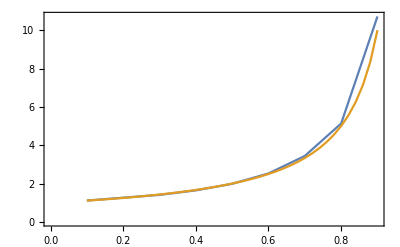

```mathematica
(* delay as a function of load *)
mu=1;
simures=Table[{la,simulatorPS[la,mu,10000,80000][[2]]},{la,0.1,0.9,0.1}];
exactres=Table[{la,1/(mu-la)},{la,0.1,0.9,0.02}];
ListLinePlot[{simures,exactres},Frame->True]
```

```mathematica
simulator2classPS[la1_,la2_,mu1_,mu2_,iniTrans_,simuLen_]:=Module[{simTime,meanqlen,prevEvTime,nextArr,nextDep,joblist1,joblist2,delsum1,delsum2,nofsamples1,nofsamples2,nn1,nn2,depInd,deptime1,deptime2,i,latot},
simTime=0;
latot=la1+la2;
nextArr=RandomVariate[ExponentialDistribution[latot]];
nextDep=Infinity;
joblist1={};
joblist2={};
meanqlen=0;
delsum1=0;
delsum2=0;
nofsamples1=0;
nofsamples2=0;
nn1=0; (* nof flows for class 1 *)
nn2=0; (* nof flows for class 2 *)
While[simTime≤simuLen,
If[nextArr<nextDep,
{
prevEvTime=simTime;
simTime=nextArr;
meanqlen+=(nn1+nn2)*(Min[simTime,simuLen]-prevEvTime);
(* serve flows *)
If[nn1>0,
For[i=1,i≤Length[joblist1],i++,
joblist1[[i,2]]=joblist1[[i,2]]-(simTime-prevEvTime)/(nn1+nn2)]
,joblist1={}];
If[nn2>0,
For[i=1,i≤Length[joblist2],i++,
joblist2[[i,2]]=joblist2[[i,2]]-(simTime-prevEvTime)/(nn1+nn2)]
,joblist2={}];
(* insert new arrival *)
If[RandomReal[]<la1/(la1+la2),{
joblist1=Append[joblist1,{simTime,RandomVariate[ExponentialDistribution[mu1]]}];
joblist1=Sort[joblist1,#1[[2]]<#2[[2]]&];
nn1++;
},{
joblist2=Append[joblist2,{simTime,RandomVariate[ExponentialDistribution[mu2]]}];
joblist2=Sort[joblist2,#1[[2]]<#2[[2]]&];
nn2++;
}
];
(* update arrival event *)
nextArr=simTime+RandomVariate[ExponentialDistribution[latot]];
(* update departure event, there is at least 1 flow in system *)
If[nn1>0,deptime1=simTime+joblist1[[1,2]]*(nn1+nn2),deptime1=Infinity];
If[nn2>0,deptime2=simTime+joblist2[[1,2]]*(nn1+nn2),deptime2=Infinity];
If[deptime1<deptime2,
nextDep=deptime1;
depInd=1;
,
nextDep=deptime2;
depInd=2;
];
},
{
prevEvTime=simTime;
simTime=nextDep;
meanqlen+=(nn1+nn2)*(Min[simTime,simuLen]-prevEvTime);
(* serve flows *)
If[nn1>0,
For[i=1,i≤Length[joblist1],i++,
joblist1[[i,2]]=joblist1[[i,2]]-(simTime-prevEvTime)/(nn1+nn2)]
,joblist1={}];
If[nn2>0,
For[i=1,i≤Length[joblist2],i++,
joblist2[[i,2]]=joblist2[[i,2]]-(simTime-prevEvTime)/(nn1+nn2)]
,joblist2={}];
(* collect statistics *)
If[depInd==1,
If[simTime>iniTrans,
delsum1+=(simTime-joblist1[[1,1]]);
nofsamples1++;
];
joblist1=Delete[joblist1,1];
nn1--;
,
If[simTime>iniTrans,
delsum2+=(simTime-joblist2[[1,1]]);
nofsamples2++;
];
joblist2=Delete[joblist2,1];
nn2--;
];
(* update departure event, now system may be totally empty *)
If[nn1>0,deptime1=simTime+joblist1[[1,2]]*(nn1+nn2),deptime1=Infinity];
If[nn2>0,deptime2=simTime+joblist2[[1,2]]*(nn1+nn2),deptime2=Infinity];
If[(nn1+nn2)>0,
If[deptime1<deptime2,
nextDep=deptime1;
depInd=1;
,
nextDep=deptime2;
depInd=2;
],
nextDep=Infinity
]
}
];
(*Print[joblist1];
Print[joblist2];*)
];
{meanqlen/(latot*simuLen),(delsum1+delsum2)/(nofsamples1+nofsamples2),delsum1/nofsamples1,delsum2/nofsamples2}
]
```

```mathematica
la1=0.4;
la2=0.15;
mu1=1;
mu2=0.5;
rho=la1/mu1+la2/mu2
simulator2classPS[la1,la2,mu1,mu2,10000,150000]
```

0.7

{4.14766,4.18813,3.27085,6.63517}

```mathematica
(* Exact result *)
{(1/mu1)/(1-rho),(1/mu2)/(1-rho)}
```

{3.33333,6.66667}